# Paschen Curve Monte Carlo Simulations

## William Bowers Eastside Preparatory School Kirkland, WA In collaboration with Sophie Gershaft, Dr. Charles Whitmer, and Gunnar Mein

## Parallel plate MCs

```mathematica
AvgElectronsBanked[Nc_,Ni_,count_] := Module[{result,stack},
stack = CreateDataStructure["Stack"];
result = Table[
Module[{pos1,pos2,numElectrons, lambdaI},
numElectrons = 1; 
stack["Push",0];
While[! stack["EmptyQ"],
pos1 = stack["Pop"];
While[(pos2 = pos1+RandomVariate[ExponentialDistribution[1]])≤Nc, 
lambdaI =Nc / Ni;
If[(pos2 - pos1) ≥ lambdaI,numElectrons++;stack["Push",pos2] ];
Sow[pos2];
pos1 = pos2];]; 
numElectrons],
{count}];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

```mathematica
AvgElectronsWeighted[Nc_,Ni_,count_] := Module[{result},
result = Table[
Module[{pos1,pos2,numElectrons, lambdaI, weight},
numElectrons = 1; 
pos1 = 0;
weight = 1;
While[(pos2 = pos1+RandomVariate[ExponentialDistribution[1]])≤Nc, 
lambdaI =Nc / Ni;
If[(pos2 - pos1) ≥ lambdaI,numElectrons+=weight;weight*=2];
pos1 = pos2];
numElectrons],
{count}];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

```mathematica
GetTime[s_,vx_,vw_,ax_]:= Module[{set,start},
If[vw > 1,
S[t_]:=1/(2ax)*((vx+ax t)Sqrt[vw^2+(vx+ax t)^2]-vx Sqrt[vw^2+vx^2]+vw^2(ArcSinh[(ax t + vx)/vw]-ArcSinh[vx/vw])),
S[t_] :=(-vx Sqrt[vx^2]+(ax t + vx)Sqrt[(ax t + vx)^2])/(2ax)
];
set = FindRoot[S[t]==s,{t,10^-15.5}];
t/.set]
```

```mathematica
GetVelocity[E_,cosθ_,ϕ_,vx0_,vy0_,vz0_,Δx_]:=Module[{v0,q,m,ax,e0,e1,v1,vx,vy,vz},
q = 1.60217662 × 10^(-19);
m = 9.10938356 × 10^(-31);
v0=Sqrt[vx0^2+vy0^2+vz0^2];
e0=1/2m v0^2;
e1 = e0+q E(Δx);
v1=Sqrt[(2 e1)/m];
vx = v1 cosθ Cos[ϕ];
vy = v1 Cos[ϕ] Sqrt[1-cosθ^2];
vz=v1 Sin[ϕ];
{vx,vy,vz}]
```

```mathematica
SubtractUI[E_,cosθ_,ϕ_,vx0_,vy0_,vz0_,Ui_]:=Module[{v0,q,m,ax,e,v1,vx,vy,vz},
q = 1.60217662 × 10^(-19);
m = 9.10938356 × 10^(-31);
v0=Sqrt[vx0^2+vy0^2+vz0^2];
e=1/2m v0^2-q Ui;
If[e<0,e=0];
v1=Sqrt[(2 e)/m];
vx = v1 cosθ Cos[ϕ];
vy = v1 Cos[ϕ] Sqrt[1-cosθ^2];
vz=v1 Sin[ϕ];
{vx,vy,vz}]
```

```mathematica
GetNewPositions[E_,s_,vx_,vy_,vz_]:=Module[{vw,q,m,ax,set,x,y,z,t,velocities},
vw=Sqrt[vy^2+vz^2];
q = 1.60217662 × 10^(-19);
m = 9.10938356 × 10^(-31);
ax=(q E)/m;
t=GetTime[s,vx,vw,ax];
x =  vx t + 1/2 ax t^2; 
y = vy t;
z=vz t;
{x,y,z}]
```

```mathematica
AvgElectrons3D[D_,V_,Ui_,Nc_,count_] := Module[{λ,λi,q,result,stack},
λ=D/Nc;
λi=(Ui D)/V;
q = 1.60217662 × 10^(-19);
stack = CreateDataStructure["Stack"];
result = Table[
Module[{x0,x1,y0,y1,z0,z1,numElectrons,cosθ,ϕ,ionized,s,vx,vy,vz},
numElectrons = 1; 
stack["Push",{0,0,0,0,0,0}];
While[! stack["EmptyQ"],
{x0,y0,z0,vx,vy,vz}=stack["Pop"];
cosθ=1;
ϕ=0;
ionized = False;
While[
s=RandomVariate[ExponentialDistribution[λ]];
{x1,y1,z1}={x0,y0,z0}+GetNewPositions[V/D,s,vx,vy,vz];
{vx,vy,vz}=GetVelocity[V/D,cosθ,ϕ,vx,vy,vz,x1-x0];
0≤x1≤D,
If[x1-x0≥λi,
numElectrons++;
{vx,vy,vz}=SubtractUI[V/D,cosθ,ϕ,vx,vy,vz,Ui];
cosθ = 1-2(RandomReal[]);
ϕ=RandomReal[2Pi];
stack["Push",{x1,y1,z1,0,0,0}],
ionized = False;
cosθ = 1-2(RandomReal[]);
ϕ=RandomReal[2Pi];
];
{x0,y0,z0}={x1,y1,z1};
];
]; 
numElectrons],
{count}];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

## Parallel plate experiments

```mathematica
r=Reap[AvgElectrons3D[10,1,1,10,1]];
ListLinePlot3D[r[[2]]]
```

-Graphics3D-

{{1/2,1},{1,1},{3/2,1.220.04},{2,1.370.05},{5/2,1.630.06},{3,1.680.07},{7/2,2.020.09},{4,2.570.10},{9/2,2.900.10},{5,3.180.12},{11/2,4.130.17},{6,4.390.18},{13/2,5.110.22},{7,5.900.26},{15/2,6.470.29},{8,8.80.4}}

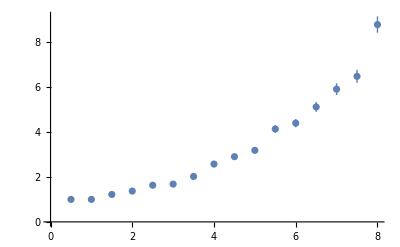

```mathematica
Table[{d,AvgElectrons3D[d,d,1,d,100]},{d,1/2,8,1/2}]
ListPlot[%]
```

{{1/4,1},{3/4,1},{5/4,1},{7/4,1},{9/4,1.0300.017},{11/4,1.1100.031},{13/4,1.1200.033},{15/4,1.200.04},{17/4,1.300.05},{19/4,1.380.05},{21/4,1.370.05},{23/4,1.510.06},{25/4,1.680.07},{27/4,1.740.07},{29/4,1.700.08},{31/4,1.920.08}}

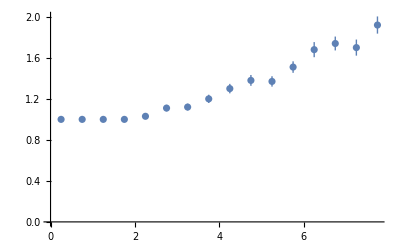

```mathematica
Table[{d,AvgElectrons3D[d,1/2d,1,d,100]},{d,1/4,8,1/2}]
ListPlot[%]
```

```mathematica
t1=Table[{d,AvgElectrons3D[d,d,1,d,1000]},{d,1/4,10,1/4}]
t2=Table[{nc,AvgElectronsBanked[nc,nc,1000]},{nc,1/4,10,1/4}]
t3=Table[{nc,AvgElectronsWeighted[nc,nc,1000]},{nc,1/4,10,1/4}]
```

{{1/4,1},{1/2,1},{3/4,1},{1,1},{5/4,1.0910.009},{3/2,1.1870.012},{7/4,1.2870.014},{2,1.3930.015},{9/4,1.4700.016},{5/2,1.6090.018},{11/4,1.7010.020},{3,1.8390.022},{13/4,1.9480.023},{7/2,2.1200.026},{15/4,2.2650.029},{4,2.4490.031},{17/4,2.6290.034},{9/2,2.850.04},{19/4,3.080.04},{5,3.240.04},{21/4,3.600.05},{11/2,3.850.05},{23/4,4.090.05},{6,4.410.06},{25/4,4.910.06},{13/2,5.220.07},{27/4,5.780.08},{7,6.140.08},{29/4,6.650.09},{15/2,7.260.10},{31/4,7.750.11},{8,8.380.11},{33/4,9.140.12},{17/2,9.840.13},{35/4,10.890.14},{9,11.560.15},{37/4,12.270.16},{19/2,13.380.19},{39/4,14.970.21},{10,15.820.20}}

{{1/4,1},{1/2,1},{3/4,1},{1,1},{5/4,1.0920.009},{3/2,1.1770.012},{7/4,1.2860.014},{2,1.3720.015},{9/4,1.4630.016},{5/2,1.5710.018},{11/4,1.6750.020},{3,1.7890.021},{13/4,1.9350.023},{7/2,2.0730.026},{15/4,2.2540.028},{4,2.4000.031},{17/4,2.5310.033},{9/2,2.7180.035},{19/4,2.940.04},{5,3.080.04},{21/4,3.450.04},{11/2,3.640.05},{23/4,3.840.05},{6,4.200.06},{25/4,4.490.06},{13/2,4.780.07},{27/4,5.230.07},{7,5.450.07},{29/4,6.000.08},{15/2,6.310.09},{31/4,6.910.10},{8,7.350.10},{33/4,7.740.11},{17/2,8.440.12},{35/4,9.060.13},{9,9.660.13},{37/4,10.370.14},{19/2,10.810.15},{39/4,11.930.17},{10,12.330.18}}

{{1/4,1},{1/2,1},{3/4,1},{1,1},{5/4,1.0980.009},{3/2,1.1800.012},{7/4,1.2740.014},{2,1.3810.015},{9/4,1.4620.017},{5/2,1.5720.019},{11/4,1.6580.021},{3,1.8150.023},{13/4,1.9190.026},{7/2,2.0330.029},{15/4,2.1440.031},{4,2.400.04},{17/4,2.550.04},{9/2,2.760.04},{19/4,2.930.05},{5,3.200.05},{21/4,3.350.06},{11/2,3.660.06},{23/4,3.780.07},{6,4.200.08},{25/4,4.560.08},{13/2,4.670.09},{27/4,5.290.11},{7,5.500.11},{29/4,5.700.12},{15/2,6.240.13},{31/4,6.700.14},{8,7.450.16},{33/4,8.210.20},{17/2,8.090.19},{35/4,9.030.22},{9,9.490.21},{37/4,10.040.24},{19/2,11.400.30},{39/4,12.230.30},{10,12.290.30}}

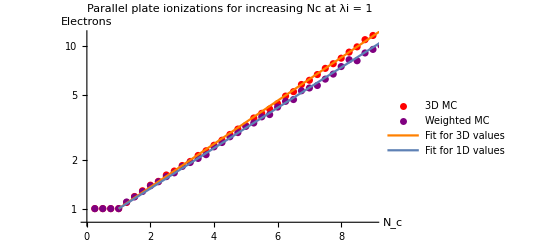

```mathematica
Show[ListLogPlot[t1, PlotLegends->{"3D MC"},PlotStyle->Red],ListLogPlot[t3,PlotStyle->Purple,PlotLegends->{"Weighted MC"}],LogPlot[Exp[0.305(x-1)],{x,1,10},PlotStyle->Orange,PlotLegends->{"Fit for 3D values"}],LogPlot[Exp[0.285(x-1)],{x,1,10},PlotLegends->{"Fit for 1D values"}],AxesLabel->{Subscript[N,c], Electrons},PlotLabel->"Parallel plate ionizations for increasing Nc at λi = 1"]
```

## Looking for curvature (ensuring exponential growth)

```mathematica
listForFit1 = {#[[1]],Log[#[[2,1]]]}&/@t1
error1=#[[2,2]]&/@t1
f1=LinearModelFit[listForFit1,{x^2, x},x,Weights->1/error1^2]
```

{{5/4,0.0870947},{3/2,0.171429},{7/4,0.252314},{2,0.33146},{9/4,0.385262},{5/2,0.475613},{11/4,0.531216},{3,0.609222},{13/4,0.666803},{7/2,0.751416},{15/4,0.817575},{4,0.89568},{17/4,0.966604},{9/2,1.04837},{19/4,1.12428},{5,1.17496},{21/4,1.28066},{11/2,1.34677},{23/4,1.40806},{6,1.48297},{25/4,1.59046},{13/2,1.65307},{27/4,1.7544},{7,1.81401},{29/4,1.89507},{15/2,1.98238},{31/4,2.04808},{8,2.12621},{33/4,2.21211},{17/2,2.28635},{35/4,2.38812},{9,2.44729}}

{0.00909955,0.0123363,0.0143121,0.0154528,0.0164125,0.0180678,0.02,0.0216691,0.0234488,0.0264632,0.0285235,0.0311829,0.033593,0.0374272,0.0412021,0.0430722,0.0463287,0.0509271,0.0529628,0.0585542,0.0648488,0.0700727,0.0775346,0.0804316,0.088896,0.0965076,0.109535,0.106356,0.122604,0.134213,0.144736,0.151095}

FittedModel[-0.261248+0.284494 x+0.00158293 x^2]

```mathematica
f1["ParameterErrors"]
```

{0.00771085,0.000683413,0.00512697}

```mathematica
listForFit2= {#[[1]],Log[#[[2,1]]]}&/@t2
error2=#[[2,2]]&/@t2
f2=NonlinearModelFit[listForFit2,-a x^2+b x,{a,b},x,Weights->1/error2^2]
f2["ParameterErrors"]
```

{{5/4,0.0880109},{3/2,0.162969},{7/4,0.251537},{2,0.31627},{9/4,0.380489},{5/2,0.451712},{11/4,0.515813},{3,0.581657},{13/4,0.660107},{7/2,0.728997},{15/4,0.812706},{4,0.875469},{17/4,0.928614},{9/2,0.999896},{19/4,1.07977},{5,1.1233},{21/4,1.23721},{11/2,1.29198},{23/4,1.34547},{6,1.43556},{25/4,1.50208},{13/2,1.56381},{27/4,1.65479},{7,1.69525},{29/4,1.79109},{15/2,1.84277},{31/4,1.93311},{8,1.99524},{33/4,2.04692},{17/2,2.13286},{35/4,2.20365},{9,2.26799},{37/4,2.33863},{19/2,2.38084}}

{0.00914438,0.0120755,0.0142971,0.0152921,0.0160277,0.0180356,0.0196917,0.0209981,0.0229194,0.0260067,0.027645,0.0313526,0.0331683,0.0353231,0.0369896,0.0405588,0.0447559,0.0505268,0.0522602,0.0573453,0.0590034,0.0662998,0.0715213,0.0736663,0.0797392,0.0916723,0.0996745,0.103496,0.110746,0.119317,0.128613,0.133755,0.143467,0.15154}

FittedModel[0.126154 x+0.0178094 x^2]

{0.0019962,0.00969634}

```mathematica
listForFit3= {#[[1]],Log[#[[2,1]]]}&/@t3
error3=#[[2,2]]&/@t3
f3=NonlinearModelFit[listForFit3,-a x^2+b x,{a,b},x,Weights->1/error3^2]
f3["ParameterErrors"]
```

{{5/4,0.0934903},{3/2,0.165514},{7/4,0.242162},{2,0.322808},{9/4,0.379805},{5/2,0.452349},{11/4,0.505612},{3,0.596085},{13/4,0.651804},{7/2,0.709513},{15/4,0.762673},{4,0.873383},{17/4,0.934524},{9/2,1.01559},{19/4,1.07466},{5,1.16221},{21/4,1.21015},{11/2,1.29719},{23/4,1.32919},{6,1.43532},{25/4,1.51623},{13/2,1.5418},{27/4,1.66582},{7,1.70493},{29/4,1.74047},{15/2,1.83018},{31/4,1.90151},{8,2.00821},{33/4,2.10474},{17/2,2.09026},{35/4,2.2},{9,2.25024},{37/4,2.30668},{19/2,2.43326}}

{0.00940662,0.0121552,0.0141111,0.0153647,0.0165175,0.0189519,0.0207235,0.0232662,0.0255165,0.0290302,0.0306627,0.0362807,0.038696,0.0440206,0.0474786,0.0537315,0.0586013,0.0643651,0.0696101,0.0804181,0.0821689,0.0907651,0.111814,0.110164,0.116161,0.13145,0.140867,0.158564,0.203348,0.186838,0.221082,0.214135,0.244833,0.298453}

FittedModel[0.115081 x+0.0205213 x^2]

{0.00220732,0.0093477}

## Comparing different MCs

{{1/2,1},{1,1.230.04},{3/2,1.690.06},{2,2.110.09},{5/2,2.790.13},{3,3.550.18},{7/2,4.390.23},{4,6.090.28},{9/2,8.50.4},{5,9.50.5},{11/2,13.60.7},{6,18.70.9},{13/2,24.41.2},{7,31.81.5},{15/2,41.22.2},{8,59.32.9},{17/2,74.4.},{9,100.5.},{19/2,134.7.},{10,179.8.}}

{{1/2,1},{1,1.360.05},{3/2,1.610.07},{2,2.070.09},{5/2,2.600.11},{3,3.340.16},{7/2,4.510.25},{4,5.350.30},{9/2,6.670.31},{5,8.10.4},{11/2,11.90.6},{6,14.00.8},{13/2,19.21.0},{7,25.21.3},{15/2,28.81.7},{8,38.02.2},{17/2,52.43.0},{9,61.23.4},{19/2,78.5.},{10,91.5.}}

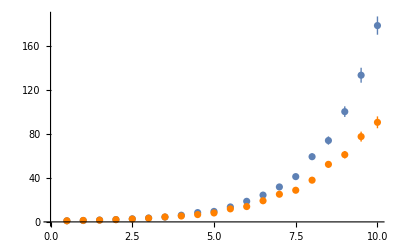

```mathematica
t1=Table[{d,AvgElectrons3D[d,2d,1,d,100]},{d,1/2,10,1/2}]
t2=Table[{nc,AvgElectronsBanked[nc,2nc,100]},{nc,1/2,10,1/2}]
Show[ListPlot[t1],ListPlot[t2,PlotStyle->Orange]]
```

{{1/2,1},{1,1},{3/2,1},{2,1},{5/2,1.0500.022},{3,1.1100.031},{7/2,1.200.04},{4,1.300.05},{9/2,1.440.05},{5,1.290.05},{11/2,1.560.07},{6,1.580.06},{13/2,1.570.07},{7,1.780.09},{15/2,1.650.08},{8,2.020.09},{17/2,2.200.10},{9,1.980.10},{19/2,2.430.12},{10,2.840.12}}

{{1/2,1},{1,1},{3/2,1},{2,1},{5/2,1.0700.026},{3,1.1200.033},{7/2,1.230.04},{4,1.300.05},{9/2,1.310.05},{5,1.440.05},{11/2,1.550.06},{6,1.560.06},{13/2,1.670.08},{7,1.850.08},{15/2,1.840.08},{8,1.870.09},{17/2,2.090.09},{9,2.030.09},{19/2,2.240.10},{10,2.500.10}}

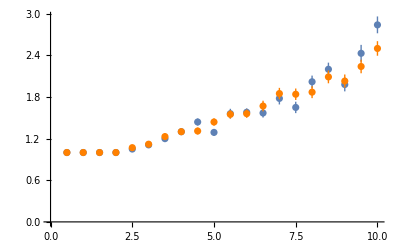

```mathematica
t1=Table[{d,AvgElectrons3D[d,1/2d,1,d,100]},{d,1/2,10,1/2}]
t2=Table[{nc,AvgElectronsBanked[nc,1/2nc,100]},{nc,1/2,10,1/2}]
Show[ListPlot[t1],ListPlot[t2,PlotStyle->Orange]]
```

## Looking at “kinks” and exponential growth

{{0.5,1},{0.75,1},{1.,1},{1.25,1.0960.013},{1.5,1.1740.017},{1.75,1.2640.020},{2.,1.3840.022},{2.25,1.4620.025},{2.5,1.5620.024},{2.75,1.6720.030},{3.,1.7760.033},{3.25,1.970.04},{3.5,2.090.04},{3.75,2.230.04},{4.,2.390.05},{4.25,2.570.06},{4.5,2.730.06},{4.75,2.920.07},{5.,3.240.08},{5.25,3.420.09},{5.5,3.710.09},{5.75,3.900.11},{6.,4.140.11},{6.25,4.660.13},{6.5,4.820.13},{6.75,4.990.14},{7.,5.630.16},{7.25,5.990.17},{7.5,6.450.20},{7.75,6.480.20},{8.,6.870.21},{8.25,8.210.27},{8.5,8.270.25},{8.75,9.430.32},{9.,9.080.28},{9.25,9.900.32},{9.5,11.10.4},{9.75,12.20.5},{10.,12.60.4}}

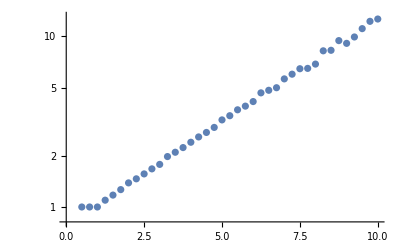

```mathematica
table = Table[{Nc,AvgElectronsWeighted[Nc,Nc,500]},{Nc,0.5,10,0.25}]
ListLogPlot[table]
```

{{0.1,1},{0.2,1},{0.3,1},{0.4,1},{0.5,1},{0.6,1},{0.7,1},{0.8,1},{0.9,1},{1.,1},{1.1,1.0400.009},{1.2,1.0780.012},{1.3,1.0980.013},{1.4,1.1200.015},{1.5,1.1800.017},{1.6,1.1980.018},{1.7,1.2460.019},{1.8,1.2900.020},{1.9,1.3300.021},{2.,1.3420.021},{2.1,1.3740.022},{2.2,1.4800.023},{2.3,1.4980.022},{2.4,1.5860.026},{2.5,1.5480.026},{2.6,1.5940.028},{2.7,1.6400.029},{2.8,1.7040.030},{2.9,1.7520.032},{3.,1.8360.033},{3.1,1.8860.035},{3.2,1.920.04},{3.3,1.930.04},{3.4,2.070.04},{3.5,2.050.04},{3.6,2.170.05},{3.7,2.130.04},{3.8,2.250.04},{3.9,2.400.05},{4.,2.340.05},{4.1,2.410.05},{4.2,2.470.05},{4.3,2.580.06},{4.4,2.740.06},{4.5,2.730.06},{4.6,2.810.06},{4.7,2.960.07},{4.8,2.870.07},{4.9,3.040.07},{5.,3.130.07}}

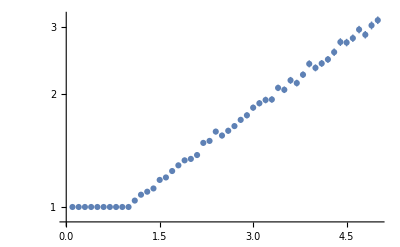

```mathematica
table2 = Table[{Nc,AvgElectronsWeighted[Nc,Nc,500]},{Nc,0.1,5,0.1}]
ListLogPlot[table2]
```

{{0.1,1},{0.2,1},{0.3,1},{0.4,1},{0.5,1},{0.6,1},{0.7,1},{0.8,1},{0.9,1},{1.,1},{1.1,1},{1.2,1},{1.3,1},{1.4,1},{1.5,1},{1.6,1},{1.7,1},{1.8,1},{1.9,1},{2.,1},{2.1,1},{2.2,1},{2.3,1},{2.4,1},{2.5,1},{2.6,1},{2.7,1},{2.8,1},{2.9,1},{3.,1},{3.1,1.00530.0007},{3.2,1.01060.0010},{3.3,1.01720.0013},{3.4,1.01890.0014},{3.5,1.02610.0016},{3.6,1.02850.0017},{3.7,1.03600.0019},{3.8,1.03770.0019},{3.9,1.04730.0021},{4.,1.04870.0022},{4.1,1.05650.0023},{4.2,1.05720.0023},{4.3,1.06300.0024},{4.4,1.06810.0025},{4.5,1.07120.0026},{4.6,1.08150.0027},{4.7,1.08740.0028},{4.8,1.09370.0029},{4.9,1.09480.0029},{5.,1.10070.0030}}

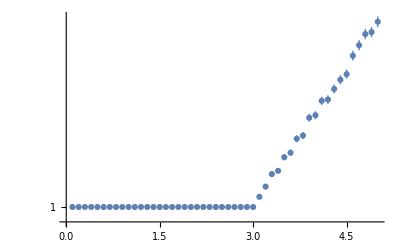

```mathematica
table3 = Table[{Nc,AvgElectronsWeighted[Nc,1/3Nc,10000]},{Nc,0.1,5,0.1}]
ListLogPlot[table3]
```

{{0.1,1},{0.2,1},{0.3,1},{0.4,1},{0.5,1},{0.6,1.0620.011},{0.7,1.1100.014},{0.8,1.1800.017},{0.9,1.2200.019},{1.,1.3200.021},{1.1,1.3360.022},{1.2,1.4120.025},{1.3,1.5040.025},{1.4,1.5820.029},{1.5,1.6760.031},{1.6,1.7080.032},{1.7,1.850.04},{1.8,1.870.04},{1.9,1.990.04},{2.,2.180.05},{2.1,2.140.05},{2.2,2.420.06},{2.3,2.380.06},{2.4,2.610.07},{2.5,2.790.08},{2.6,2.780.07},{2.7,2.920.08},{2.8,3.050.08},{2.9,2.970.08},{3.,3.480.10},{3.1,3.680.11},{3.2,3.680.11},{3.3,3.900.11},{3.4,4.050.13},{3.5,4.190.13},{3.6,4.360.13},{3.7,4.710.15},{3.8,4.750.15},{3.9,5.230.16},{4.,5.190.17},{4.1,5.710.20},{4.2,6.000.21},{4.3,5.820.19},{4.4,6.310.23},{4.5,6.930.24},{4.6,7.260.27},{4.7,8.060.29},{4.8,8.280.31},{4.9,8.300.32},{5.,8.80.4}}

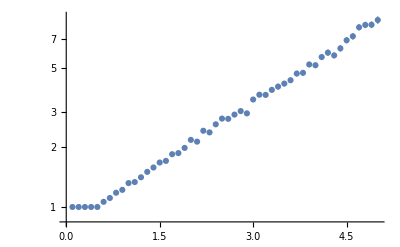

```mathematica
table4 = Table[{Nc,AvgElectronsWeighted[Nc,2Nc,500]},{Nc,0.1,5,0.1}]
ListLogPlot[table4]
```

## Exploring alpha

Generate table of electrons and find exponential growth coefficient

```mathematica
FindAlpha[λi_] := Module[{electrons,result,length,i,total,slopes,alpha,e},
electrons = Table[{Nc,AvgElectronsWeighted[Nc,((1/λi) Nc),500]},{Nc,λi+1,20,0.5}];
alpha = Mean[Table[Log[e[[2]] ]/(e[[1]] -λi),{e,electrons}]];
alpha]
```

```mathematica
alphaVals = Table[{λi,FindAlpha[λi]},{λi,1/4,4,1/2}]
alphav2Vals = Table[{λi,Exp[-λi]},{λi,1/4,4,1/2}] //N
```

{{1/4,0.66290.0027},{3/4,0.36500.0010},{5/4,0.22440.0009},{7/4,0.14110.0008},{9/4,0.09120.0008},{11/4,0.05770.0007},{13/4,0.03630.0006},{15/4,0.02210.0005}}

{{0.25,0.778801},{0.75,0.472367},{1.25,0.286505},{1.75,0.173774},{2.25,0.105399},{2.75,0.0639279},{3.25,0.0387742},{3.75,0.0235177}}

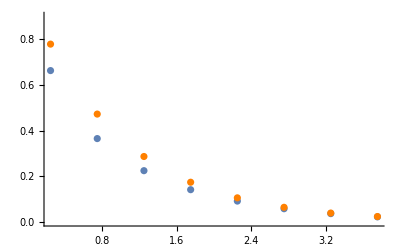

```mathematica
Show[ListPlot[alphaVals],ListPlot[alphav2Vals,PlotStyle->Orange],PlotRange->{0,0.9}]
```

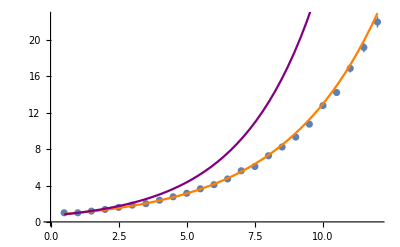

```mathematica
λi=1;
testVals = Table[{Nc,AvgElectronsWeighted[Nc,(1/λi) Nc,1000]},{Nc,1/2,12,1/2}];
α = FindAlpha[λi][[1]];
α2 = Exp[-λi];
Show[ListPlot[testVals],Plot[Exp[α (Nc-λi)],{Nc,1/2,12},PlotStyle->Orange],Plot[Exp[α2( Nc-λi)],{Nc,1/2,12},PlotStyle->Purple]]
```

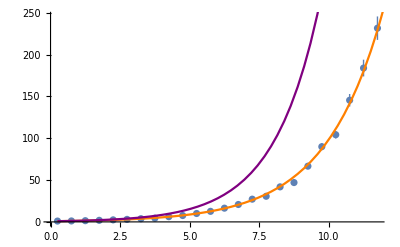

```mathematica
λi=1/2;
testVals = Table[{Nc,AvgElectronsWeighted[Nc,(1/λi) Nc,1000]},{Nc,1/4,12,1/2}];
α = FindAlpha[λi][[1]];
α2 = Exp[-λi];
Show[ListPlot[testVals],Plot[Exp[α (Nc-λi)],{Nc,1/4,12},PlotStyle->Orange],Plot[Exp[α2( Nc-λi)],{Nc,1/4,12},PlotStyle->Purple]]
```

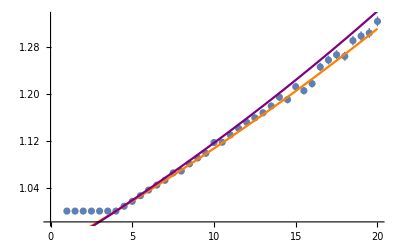

```mathematica
λi=4;
testVals = Table[{Nc,AvgElectronsWeighted[Nc,(1/λi) Nc,5000]},{Nc,1,20,1/2}];
α = FindAlpha[λi][[1]];
α2 = Exp[-λi];
Show[ListPlot[testVals],Plot[Exp[α (Nc-λi)],{Nc,1,20},PlotStyle->Orange],Plot[Exp[α2( Nc-λi)],{Nc,1,20},PlotStyle->Purple]]
```

## Alpha equation with x (reference alpha derivation)

```mathematica
Clear[α]
FindAlphav2[λi_,x_]:= (Exp[-λi] - Exp[-x])/(1-Exp[-x])
Plot3D[FindAlphav2[λi,x],{λi,1/2,4},{x,1/2,5},AxesLabel->{λi,x,α}]
```

-Graphics3D-

```mathematica
FindRoot[FindAlphav2[1/2,x]==FindAlpha[1/2][[1]],{x,1,6}]
FindRoot[FindAlphav2[1,x]==FindAlpha[1][[1]],{x,1,6}]
FindRoot[FindAlphav2[4,x]==FindAlpha[4][[1]],{x,1,6}]
```

{x→1.42628}

{x→2.16402}

{x→6.78437}

12.650.06

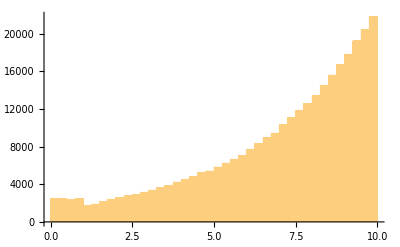

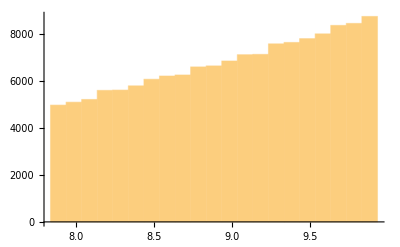

```mathematica
l1 = Reap[AvgElectronsBanked[10,10,10000]]; l1[[1]]
Histogram[l1[[2,1]],{0,10,0.25}]
Histogram[l1[[2,1]],{(10-2.16401),10,0.1}]
```

7.250.04

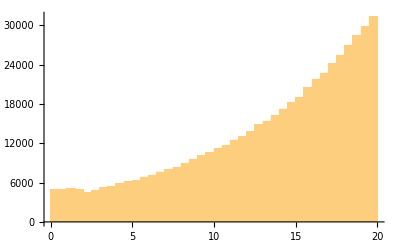

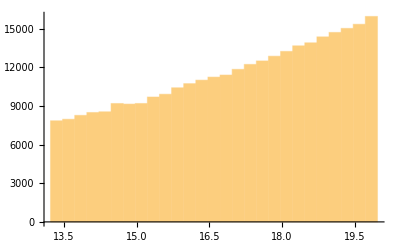

```mathematica
l2= Reap[AvgElectronsBanked[20,10,10000]]; l2[[1]]
Histogram[l2[[2,1]],{0,20,0.5}]
Histogram[l2[[2,1]],{20-6.78,20,0.25}]
```

95.40.5

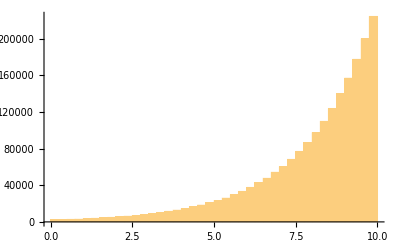

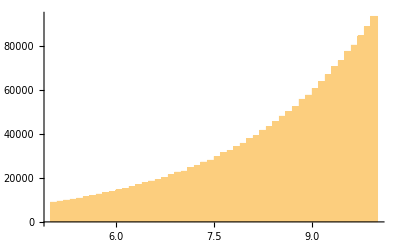

```mathematica
l3 = Reap[AvgElectronsBanked[10,20,10000]]; l3[[1]]
Histogram[l3[[2,1]],{0,10,0.25}]
Histogram[l3[[2,1]],{10-5,10,0.1}]
```

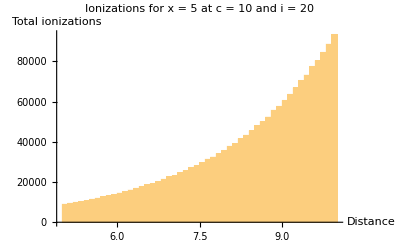

```mathematica
Histogram[l3[[2,1]],{10-5,10,0.1},AxesLabel->{"Distance", "Total ionizations"},PlotLabel->"Ionizations for x = 5 at c = 10 and i = 20"]
```

```mathematica
FindKink[λi_] := Module[{idx,electrons,positions,result,length,i,total,slopes,alpha,e},
electrons = Table[{d,AvgElectrons3D[d,((1/λi)d),1,d,100]},{d,λi/50, λi+1, 0.05}];
positions=Position[electrons,1];
idx=First[Last[positions]];
electrons[[idx,1]]];
```

```mathematica
Table[{x,FindKink[x]},{x,0.25,5.75,0.5}]
```

{{0.25,0.25},{0.75,0.75},{1.25,1.25},{1.75,1.75},{2.25,2.65},{2.75,2.95},{3.25,3.45},{3.75,4.05},{4.25,4.75},{4.75,5.25},{5.25,5.75},{5.75,6.25}}

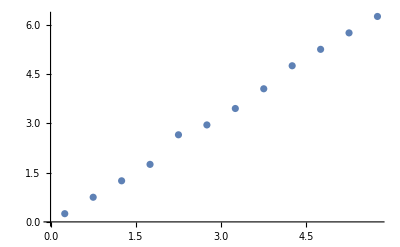

```mathematica
ListPlot[%]
```

## 3D Alphas

```mathematica
FindAlpha3D[λi_] := Module[{electrons,result,length,i,total,slopes,alpha,e,r},
r=FindKink[λi];
electrons = Table[{d,AvgElectrons3D[d,((1/λi) d),1,d,500]},{d,r+1,r+5,0.5}];
alpha = Mean[Table[Log[e[[2]] ]/(e[[1]] -r),{e,electrons}]];
{alpha,r}]
```

```mathematica
Table[{x,FindAlpha3D[x][[1]]},{x,1/2,2,1/2}]
```

{{1/2,0.5300.005},{1,0.3090.005},{3/2,0.1860.006},{2,0.1220.005}}

```mathematica
Table[{x,FindAlpha3D[x][[1]]},{x,5/2,5,1/2}]
```

{{5/2,0.0710.005},{3,0.0430.004},{7/2,0.0320.006},{4,0.0250.005},{9/2,0.00840.0025},{5,0.0210.007}}

```mathematica
alphas3d={{1/2,0.5300.005},{1,0.3090.005},{3/2,0.1860.006},{2,0.1220.005},{5/2,0.0710.005},{3,0.0430.004},{7/2,0.0320.006},{4,0.0250.005}}
```

{{1/2,0.5300.005},{1,0.3090.005},{3/2,0.1860.006},{2,0.1220.005},{5/2,0.0710.005},{3,0.0430.004},{7/2,0.0320.006},{4,0.0250.005}}

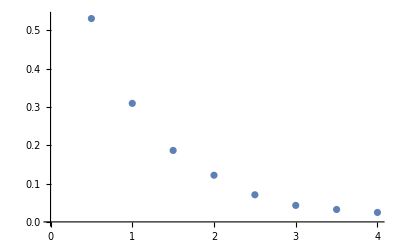

```mathematica
ListPlot[alphas3d]
```

```mathematica
(*taken from earlier calculation*)
alphas1d={{1/2,0.48010.0013},{1,0.28540.0009},{3/2,0.17950.0008},{2,0.11150.0008},{5/2,0.07100.0007},{3,0.04560.0006},{7/2,0.02870.0005},{4,0.01790.0005}}
```

{{1/2,0.48010.0013},{1,0.28540.0009},{3/2,0.17950.0008},{2,0.11150.0008},{5/2,0.07100.0007},{3,0.04560.0006},{7/2,0.02870.0005},{4,0.01790.0005}}

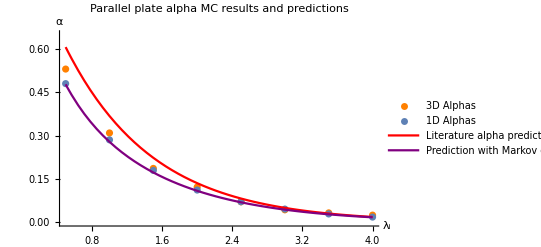

```mathematica
Show[ListPlot[alphas3d,PlotStyle->Orange,PlotLegends->{"3D Alphas"}],ListPlot[alphas1d,PlotLegends->{"1D Alphas"}],Plot[Exp[-x],{x,1/2,4},PlotStyle->Red,PlotLegends->{"Literature alpha prediction"}],Plot[AlphaPrediction[x],{x,1/2,4},PlotStyle->Purple,PlotLegends->{"Prediction with Markov chain"}],AxesLabel->{Subscript[λ,i],α},PlotLabel->"Parallel plate alpha MC results and predictions",PlotRange->{0,0.65}]
```

```mathematica
AlphaPrediction[r_]:= ProductLog[r Exp[-r]]/r;
```

## Plotting parallel plate breakdown values

```mathematica
FindBreakdown[r_,γ_] := Module[{alpha, idx,Nc, Ni},
alpha = FindAlpha[r][[1]];
Nc = Log[γ]/alpha + r ;
Ni = (1/r)(Nc);
{Nc,Ni}]
```

```mathematica
bdVals = Table[FindBreakdown[r,50],{r,1/50,5,1/4}]
```

{{4.1640.024,208.21.2},{6.3750.020,23.610.08},{8.8350.023,16.990.04},{11.7000.031,15.190.04},{15.050.05,14.760.04},{19.040.07,14.990.05},{24.090.11,15.850.07},{29.820.16,16.850.09},{37.480.25,18.550.12},{47.10.4,20.750.17},{59.10.6,23.450.22},{71.00.8,25.650.29},{92.21.2,30.50.4},{119.11.9,36.40.6},{145.12.7,41.20.8},{189.4.,50.11.1},{234.6.,58.31.5},{292.8.,68.31.9},{369.13.,81.62.8},{476.19.,100.4.}}

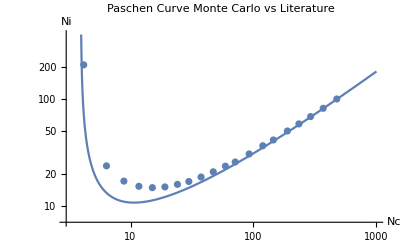

```mathematica
Show[LogLogPlot[Nc/(Log[Nc]-Log[Log[51]]),{Nc,3.9,1000},PlotRange->{{3,1000},{7,400}}],ListLogLogPlot[bdvals],AxesLabel->{"Nc","Ni"},PlotLabel->"Paschen Curve Monte Carlo vs Literature"]
```

```mathematica
FindBreakdown3D[r_,γ_] := Module[{alpha,idx, Nc, Ni},
{alpha,idx} = FindAlpha3D[r];
Nc = Log[γ]/alpha + idx ;
Ni = (1/r)(Nc);
{Nc,Ni}]
```

```mathematica
bd3d=Table[FindBreakdown3D[r,50],{r,1/50,5,1/4}]
```

{{3.3580.020,167.91.0},{5.9580.034,22.070.13},{8.320.05,15.990.10},{11.040.08,14.340.10},{14.400.12,14.120.12},{17.900.19,14.090.15},{22.670.30,14.920.20},{28.30.5,15.980.26},{34.10.7,16.880.33},{45.51.1,20.00.5},{54.41.5,21.60.6},{65.42.1,23.60.8},{88.23.5,29.21.2},{88.63.5,27.11.1},{133.7.,37.91.9},{153.9.,40.52.3},{202.13.,50.23.3},{233.17.,55.4.},{282.23.,62.5.},{384.37.,80.8.}}

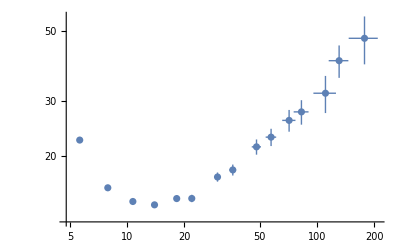

```mathematica
ListLogLogPlot[bd]
```

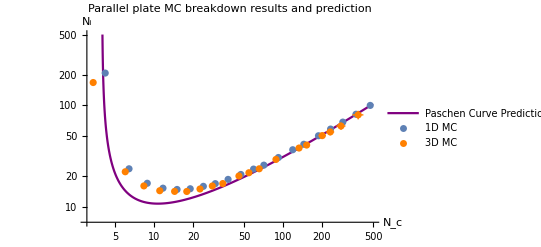

```mathematica
Show[LogLogPlot[Nc/(Log[Nc]-Log[Log[51]]),{Nc,3.9,500},PlotRange->{{3,500},{7,500}},PlotStyle->Purple,PlotLegends->{"Paschen Curve Prediction"}],
ListLogLogPlot[bd2d,PlotLegends->{"1D MC"}],
ListLogLogPlot[bd3d,PlotStyle->Orange,PlotLegends->{"3D MC"}],
PlotLabel->"Parallel plate MC breakdown results and prediction",AxesLabel->{Subscript[N,c],Subscript[N,i]},ScalingFunctions->{"None","Log"}]
```

## Concentric sphere MCs

```mathematica
SSGetNewPositions[s_,k_,x0_,y0_,z0_,vx0_,vy0_,vz0_,cosθ_,ϕ_,ionized_]:=Module[{q,m,path,eField,Δt,R,x,y,z,vx,vy,vz},
q = 1.60217662 × 10^(-19);
m = 9.10938356 × 10^(-31);
{x,y,z}={x0,y0,z0};
{vx,vy,vz}=SSGetVelocity[vx0,vy0,vz0,cosθ,ϕ,ionized];
path=0;
Δt=0.00000001;
While[path<s,
R=Sqrt[x^2+y^2+z^2];
{x,y,z}+=Δt{vx,vy ,vz}; 
{vx,vy,vz}+= (Δt q k)/(m R^3){x,y,z }; 
path+=Sqrt[(vx Δt)^2+(vy Δt)^2+(vz Δt)^2];
];
{x,y,z,vx,vy,vz}]
```

```mathematica
SSGetVelocity[vx_,vy_,vz_,cosθ_,ϕ_,ionized_]:=Module[{q,m,e0,e1,v0,v1,vx1,vy1,vz1},
q = 1.60217662 × 10^(-19);
m = 9.10938356 × 10^(-31);
v0=Sqrt[vx^2+vy^2+vz^2];
If[ionized,
e0=1/2 m v0^2;
e1=e0-q;
If[e1<0,e1=0];
v1=Sqrt[2 e1/m],
v1=v0;
];
vx1 = v1 Cos[ϕ]Sqrt[1-cosθ^2];
vy1 = Sin[ϕ] Sqrt[1-cosθ^2];
vz1=v1 cosθ;
{vx1,vy1,vz1}]
```

```mathematica
SSAvgElectrons3D[a_,b_,Ni_,count_] := Module[{k,D,λi,q,result,stack},
D=b-a;
stack = CreateDataStructure["Stack"];
result = Table[
Module[{x0,y0,z0,x1,y1,z1,numElectrons,cosθ,ϕ,s,vx0,vy0,vz0,vx,vy,vz,k,r0,r1,ionized},
numElectrons = 1; 
{{x0,y0,z0}}=RandomPoint[Sphere[{0,0,0},a],1];
stack["Push",{x0,y0,z0,0,0,0}];
While[! stack["EmptyQ"],
{x0,y0,z0,vx,vy,vz}=stack["Pop"];
{cosθ,ϕ}=GetAngles[x0,y0,z0];
ionized=False;
While[
s=RandomVariate[ExponentialDistribution[1]];
k=(Ni a b)(b-a);
{x1,y1,z1,vx,vy,vz}=SSGetNewPositions[s,k,x0,y0,z0,vx,vy,vz,cosθ,ϕ,ionized];
r0=Sqrt[(x0^2+y0^2+z0^2)];
r1=Sqrt[(x1^2+y1^2+z1^2)];
a≤r1≤b ,
If[(k/r0-k/r1)≥1,
{cosθ,ϕ}=GetAngles[x1,y1,z1];
ionized=True;
numElectrons++;
stack["Push",{x1,y1,z1,0,0,0}],
{cosθ,ϕ,ionized}={1-2(RandomReal[]),RandomReal[2Pi],False};
];
{x0,y0,z0}={x1,y1,z1};
];
]; 
numElectrons],
{count}];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

```mathematica
SSAvgElectrons3Dv2[a_,b_,Ni_,Nc_,count_] := Module[{k,D,λi,λ,q,result,stack},
D=b-a;
stack = CreateDataStructure["Stack"];
result = Table[
Module[{x0,y0,z0,x1,y1,z1,numElectrons,cosθ,ϕ,s,vx0,vy0,vz0,vx,vy,vz,k1,r0,r1,ionized},
numElectrons = 1; 
{{x0,y0,z0}}=RandomPoint[Sphere[{0,0,0},a],1];
stack["Push",{x0,y0,z0,0,0,0}];
While[! stack["EmptyQ"],
{x0,y0,z0,vx,vy,vz}=stack["Pop"];
{cosθ,ϕ}=GetAngles[x0,y0,z0];
ionized=False;
While[
s=RandomVariate[ExponentialDistribution[(b-a)/Nc]];
k1=(Ni a b)/(b-a);
{x1,y1,z1,vx,vy,vz}=SSGetNewPositions[s,k1,x0,y0,z0,vx,vy,vz,cosθ,ϕ,ionized];
r0=Sqrt[(x0^2+y0^2+z0^2)];
r1=Sqrt[(x1^2+y1^2+z1^2)];
a≤r1≤b ,
If[(k1/r0-k1/r1)≥1,
{cosθ,ϕ}=GetAngles[x1,y1,z1];
ionized=True;
numElectrons++;
stack["Push",{x1,y1,z1,0,0,0}],
{cosθ,ϕ,ionized}={1-2(RandomReal[]),RandomReal[2Pi],False};
];
{x0,y0,z0}={x1,y1,z1};
];
]; 
numElectrons],
{count}];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

## Concentric sphere experiments

```mathematica
r=Reap[SSAvgElectrons3D[2,5,1,1]];
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0},5]}],Graphics3D[Sphere[{0,0,0},2]],ListLinePlot3D[r[[2]]]]
```

-Graphics3D-

```mathematica
t=Table[{a,SSAvgElectrons3Dv2[a,2a,a,a,250]},{a,1/4,12,1/4}]
```

{{1/4,1},{1/2,1},{3/4,1},{1,1},{5/4,1.1680.024},{3/2,1.3320.030},{7/4,1.4000.031},{2,1.4760.032},{9/4,1.5760.034},{5/2,1.760.04},{11/4,1.850.04},{3,2.010.04},{13/4,2.170.05},{7/2,2.260.05},{15/4,2.380.06},{4,2.560.06},{17/4,2.770.07},{9/2,2.840.07},{19/4,3.110.07},{5,3.530.09},{21/4,3.560.10},{11/2,3.790.09},{23/4,4.180.11},{6,4.740.12},{25/4,4.710.14},{13/2,5.020.14},{27/4,5.320.14},{7,5.690.16},{29/4,6.100.17},{15/2,6.700.18},{31/4,6.990.21},{8,7.630.21},{33/4,7.960.21},{17/2,8.870.26},{35/4,9.090.26},{9,9.760.29},{37/4,10.690.31},{19/2,11.200.31},{39/4,11.430.34},{10,13.40.4},{41/4,13.70.4},{21/2,15.20.4},{43/4,15.90.4},{11,16.90.5},{45/4,18.10.5},{23/2,18.90.6},{47/4,20.40.6},{12,22.40.7}}

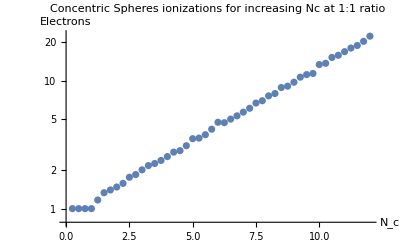

```mathematica
ListLogPlot[t,AxesLabel->{Subscript[N,c],Electrons},PlotLabel->"Concentric Spheres ionizations for increasing Nc at 1:1 ratio"]
```

## Looking for curvature (ensuring exponential growth)

```mathematica
listForFitCC = {#[[1]],Log[#[[2,1]]]}&/@t
errorCC=#[[2,2]]&/@t
fCC=NonlinearModelFit[listForFitCC,-a x^2+b x,{a,b},x,Weights->1/errorCC^2]
fCC["CovarianceMatrix"]
```

{{5/4,0.14842},{3/2,0.255417},{7/4,0.349247},{2,0.402795},{9/4,0.489193},{5/2,0.546386},{11/4,0.616266},{3,0.676001},{13/4,0.771496},{7/2,0.824175},{15/4,0.90987},{4,0.945461},{17/4,1.0289},{9/2,1.09393},{19/4,1.15877},{5,1.23489},{21/4,1.2692},{11/2,1.38053},{23/4,1.4161},{6,1.50052},{25/4,1.54863},{13/2,1.6662},{27/4,1.68362},{7,1.76216},{29/4,1.80006},{15/2,1.88813},{31/4,1.95359},{8,2.01969},{33/4,2.09924},{17/2,2.18313},{35/4,2.24728},{9,2.29455},{37/4,2.35878},{19/2,2.44513},{39/4,2.51122},{10,2.55373},{41/4,2.64582},{21/2,2.69524},{43/4,2.77259},{11,2.84188},{45/4,2.89021},{23/2,2.95736},{47/4,3.0265},{12,3.07325}}

{0.0115989,0.014371,0.0156051,0.0158188,0.0164654,0.0167556,0.0194029,0.0212908,0.0234303,0.025184,0.0287849,0.0309755,0.0329892,0.0343363,0.0379057,0.0424966,0.0443238,0.0490599,0.0548942,0.0600279,0.0622403,0.0660538,0.0715394,0.0795154,0.0814379,0.0903477,0.0971108,0.106358,0.118653,0.118694,0.130344,0.144404,0.154563,0.165525,0.176921,0.185247,0.199318,0.221037,0.224549,0.253184,0.269848,0.282382,0.301625,0.319853}

FittedModel[0.196308 x+0.00779103 x^2]

{{1.4045×10^-6,6.64408×10^-6},{6.64408×10^-6,0.0000398125}}

## Concentric sphere alphas

```mathematica
SSFindKink[λi_] := Module[{idx,electrons,positions,result,length,i,total,slopes,alpha,e},
electrons = Table[{a,SSAvgElectrons3Dv2[a,2a,(1/λi)a,a,50]},{a,1/4,4,1/4}];
positions=Position[electrons,1];
idx=First[Last[positions]];
electrons[[idx,1]]];
```

{{1/4,1},{1/2,1},{3/4,1},{1,1},{5/4,1},{3/2,1},{7/4,1},{2,5/4},{9/4,5/4},{5/2,5/4},{11/4,5/4},{3,5/4},{13/4,5/4},{7/2,3/2},{15/4,3/2},{4,3/2}}

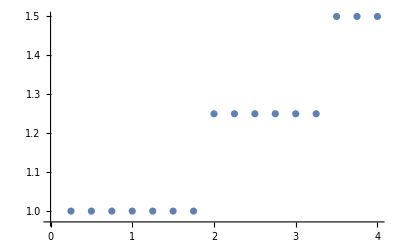

```mathematica
Table[{r,SSFindKink[r]},{r,1/4,4,1/4}]
ListPlot[%]
```

{{1/4,0.5},{1/2,0.75},{3/4,0.75},{1,1.},{5/4,1.},{3/2,1.},{7/4,1.},{2,1.25},{9/4,1.25},{5/2,1.25},{11/4,1.25},{3,1.25},{13/4,1.25},{7/2,1.5},{15/4,1.5},{4,1.5}}

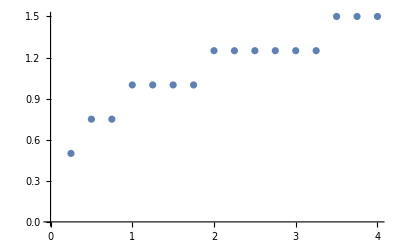

```mathematica
Table[{r,SSFindKink[r]},{r,1/4,4,1/4}]
ListPlot[%]
```

```mathematica
SSFindAlpha3D[λi_,reps_] := Module[{idx,electrons,positions,result,length,i,total,slopes,alpha,e},
idx=SSFindKink[λi];
electrons = Table[{a,SSAvgElectrons3Dv2[a,2a,(1/λi)a,a,reps]},{a,idx+1/2,idx+5/2,1/2}];
alpha = Mean[Table[Log[e[[2]] ]/(e[[1]] -idx),{e,electrons}]];
{alpha,idx}]
```

```mathematica
Table[{λi,SSFindAlpha3D[λi,200] [[1]]},{λi,1/4,5,1/2}]
```

{{1/4,1.1950.019},{3/4,0.5690.011},{5/4,0.3250.012},{7/4,0.2160.011},{9/4,0.1800.011},{11/4,0.1070.009},{13/4,0.1020.009},{15/4,0.0450.006},{17/4,0.0270.005},{19/4,0.00730.0020}}

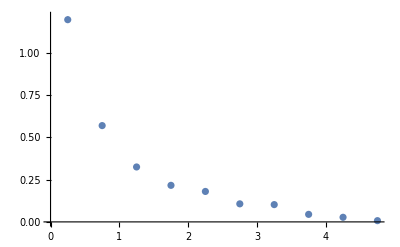

```mathematica
ListPlot[%]
```

## Plotting breakdown for concentric spheres

```mathematica
SSFindBreakdown3D[r_,γ_,reps_] := Module[{alpha,idx, Nc, Ni},
{alpha,idx} = SSFindAlpha3D[r,reps];
Nc = Log[γ]/alpha + idx ;
Ni = (1/r)(Nc);
{Nc,Ni}]
```

```mathematica
ssbd=Table[SSFindBreakdown3D[r,500,1000],{r,1/15,4,1/4}]
```

```mathematica
{{4.7120.028,70.70.4},{6.910.04,21.840.14},{9.770.07,17.250.13},{13.110.12,16.050.15},{18.780.27,17.610.25},{22.20.4,16.890.27},{27.30.5,17.430.33},{31.50.7,17.40.4},{40.21.0,19.40.5},{46.81.4,20.20.6},{51.21.6,18.20.6},{68.72.7,22.40.9},{112.6.,33.71.7},{137.8.,38.32.2}}
```

{{4.7120.028,70.70.4},{6.910.04,21.840.14},{9.770.07,17.250.13},{13.110.12,16.050.15},{18.780.27,17.610.25},{22.20.4,16.890.27},{27.30.5,17.430.33},{31.50.7,17.40.4},{40.21.0,19.40.5},{46.81.4,20.20.6},{51.21.6,18.20.6},{68.72.7,22.40.9},{112.6.,33.71.7},{137.8.,38.32.2}}

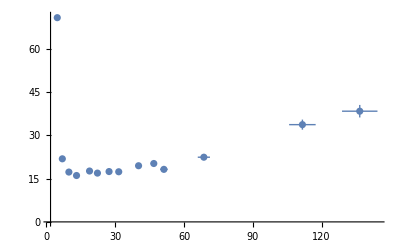

```mathematica
ListPlot[ssbd,PlotRange->All]
```

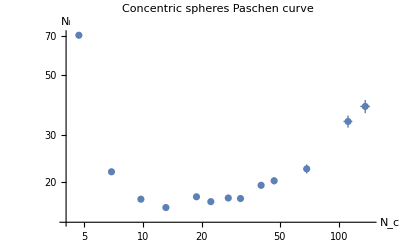

```mathematica
ListLogLogPlot[ssbd,PlotLabel->"Concentric spheres Paschen curve",AxesLabel->{Subscript[N,c],Subscript[N,i]}]
```

## Sphere-in-cylinder MCs

```mathematica
SCGetNewPositions[Ni_,s_,a_,b_,h_,potential_,x0_,y0_,z0_,vx0_,vy0_,vz0_,cosθ_,ϕ_,ionized_]:=Module[{q,m,path,Δt,x,y,z,vx,vy,vz,ex,ey,ez,Δ,count},
q = 1.60217662 × 10^(-19);
m = 9.10938356 × 10^(-31);
{x,y,z}={x0,y0,z0};
{vx,vy,vz}=SCGetVelocity[vx0,vy0,vz0,cosθ,ϕ,ionized];
path=0;
Δt=0.0000001;
Δ=0.000000000001;
count=0;
While[ path<s ,
If[!(a<Sqrt[x^2+y^2+z^2]<b-0.01&& -h/2<=z<=h/2),Return[{100,100,100,0,0,0}]];
{ex,ey,ez}={-(Ni potential[x+Δ,y,z]-Ni potential[x,y,z])/Δ,-(Ni potential[x,y+Δ,z]-Ni potential[x,y,z])/Δ,-(Ni potential[x,y,z+Δ]-Ni potential[x,y,z])/Δ};
{x,y,z}+=Δt{vx,vy ,vz}; 
{vx,vy,vz}+= ((q Δt)/m){ex,ey,ez }; 
(*Sow[{x,y,z}];*)
path+=Sqrt[(Δt vx)^2+(Δt vy)^2+(Δt vz)^2];
count++;
];
{x,y,z,vx,vy,vz}]
```

```mathematica
SCGetVelocity[vx_,vy_,vz_,cosθ_,ϕ_,ionized_]:=Module[{q,m,e0,e1,v0,v1,vx1,vy1,vz1},
q = 1.60217662 × 10^(-19);
m = 9.10938356 × 10^(-31);
v0=Sqrt[vx^2+vy^2+vz^2];
If[ionized,
e0=1/2 m v0^2;
e1=e0-q;
If[e1<0,e1=0];
v1=Sqrt[2 e1/m],
v1=v0;
];
vx1 = v1 Cos[ϕ]Sqrt[1-cosθ^2];
vy1 = Sin[ϕ] Sqrt[1-cosθ^2];
vz1=v1 cosθ;
{vx1,vy1,vz1}]
```

```mathematica
FindBinNum[costheta_,binwidth_]:=Floor[(costheta+1)/binwidth]+1
```

```mathematica
GetAngles[x_,y_,z_] := {z/Sqrt[x^2+y^2+z^2],ArcTan[x,y]}
```

```mathematica
SCAvgElectrons3D[potential_,a_,b_,h_,Ni_,binwidth_,lmax_,count_] := Module[{countbin,electronsbin,squaredbin,D,q,result,stack,region,lapl,lbin,lbinSquared,data},
countbin = Table[0,2/binwidth];
electronsbin =  Table[0,2/binwidth];
squaredbin= Table[0,2/binwidth];
lbin = Table[0,lmax/2+1];
lbinSquared =  Table[0,lmax/2+1,lmax/2+1];
data = {};
stack = CreateDataStructure["Stack"];
result = Table[
Module[{x0,y0,z0,x1,y1,z1,numElectrons,currcosθ,currϕ,cθ0,ϕ0,s,vx0,vy0,vz0,vx,vy,vz,r,ionized,z,idx,SH,l,l2},
numElectrons = 1; 
{{x0,y0,z0}}=RandomPoint[Sphere[{0,0,0},a+0.000001],1];
{cθ0,ϕ0} = GetAngles[x0,y0,z0];
stack["Push",{x0,y0,z0,0,0,0}];
While[! stack["EmptyQ"],
{x0,y0,z0,vx,vy,vz}=stack["Pop"];
{currcosθ,currϕ}=GetAngles[x0,y0,z0];
ionized=False;
While[
s=RandomVariate[ExponentialDistribution[1]];
{x1,y1,z1,vx,vy,vz}=SCGetNewPositions[Ni,s,a,b,h,potential,x0,y0,z0,vx,vy,vz,currcosθ,currϕ,ionized];
(a≤Sqrt[x1^2+y1^2+z1^2]≤b&& -h/2≤z1≤h/2),
If[Ni(potential[x0,y0,z0]-potential[x1,y1,z1])≥1,
{currcosθ,currϕ}=GetAngles[x1,y1,z1];
ionized=True;
numElectrons++;
stack["Push",{x1,y1,z1,0,0,0}],
{currcosθ,currϕ,ionized}={1-2(RandomReal[]),RandomReal[2Pi],False}];
{x0,y0,z0}={x1,y1,z1}
]; 
];
idx=FindBinNum[cθ0,binwidth];
countbin[[idx]]+=1;
electronsbin[[idx]]+=numElectrons;
squaredbin[[idx]]+=numElectrons^2;
SH=numElectrons Table[Conjugate[SphericalHarmonicY[l,0,ArcCos[cθ0],ϕ0]],{l,0,lmax,2}];
AppendTo[data,{ArcCos[cθ0],ϕ0,numElectrons}];
For[l= 0, l <= lmax, l+=2,
lbin[[l/2+1]]+=SH[[l/2+1]];
For[l2=0,l2<=lmax,l2+=2,
lbinSquared[[l/2+1,l2/2+1]]+=SH[[l/2+1]]SH[[l2/2+1]]
]
];
numElectrons],
{count}];
Sow[{countbin,electronsbin, squaredbin,lbin,lbinSquared,data}];Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

## Sphere-in-cylinder experiments

```mathematica
e3=Reap[SCAvgElectrons3D[potential,2,9,18,0.2,2,0,1]]
```

{2StandardDeviation[{2}],{{{-0.00340287,0.239768,-2.03593},{-0.00340318,0.239792,-2.03614},{-0.00340387,0.239842,-2.03655},{-0.00340487,0.239915,-2.03718},{-0.00340618,0.240014,-2.03802},3614,{-3.3189,1.54059,-8.14717},{-3.31983,1.54082,-8.15394},{-3.32076,1.54105,-8.16072},{-3.32169,1.54128,-8.16752}}}}
 |  |  |  |

```mathematica
Show[Graphics3D[ {Opacity[0.3],Cylinder[{{0,0,-9},{0,0,9}},9]}],Graphics3D[Ball[{0,0,0},2]],ListLinePlot3D[e3[[2]]],Graphics3D[{Arrow[{{0,0,-2},{0,0,-9}}]}]]
```

-Graphics3D-

```mathematica
errors =Sqrt[bins[[3]]/bins[[1]] -(bins[[2]]/bins[[1]])^2]/Sqrt[2000];
electronsPart=Table[Around[(bins[[2]]/bins[[1]])[[i]],errors[[i]]],{i,1,40}];
list = bins[[6]];
fit=LinearModelFit[list,Table[SphericalHarmonicY[l,0,θ,ϕ],{l,0,8,2}],{θ,ϕ},IncludeConstantBasis->False];
Clear[t];
max=NMaximize[fit[t,0],{t,0,Pi}];
SHYs=Table[SphericalHarmonicY[l,0,t,0],{l,0,8,2}];
error = Sqrt[SHYs.fit["CovarianceMatrix"].Transpose[SHYs]]/.max[[2]];
Around[max[[1]],error]
```

9.360.07

```mathematica
electrons=Transpose[{Table[theta,{theta,-0.975,0.975,0.05}],electronsPart}]
```

{{-0.975,9.310.11},{-0.925,9.100.11},{-0.875,8.960.11},{-0.825,8.640.10},{-0.775,8.630.10},{-0.725,8.650.10},{-0.675,8.560.10},{-0.625,8.530.10},{-0.575,8.620.11},{-0.525,8.540.10},{-0.475,8.590.10},{-0.425,8.640.10},{-0.375,8.710.10},{-0.325,8.540.11},{-0.275,8.860.11},{-0.225,8.830.11},{-0.175,8.900.11},{-0.125,8.800.11},{-0.075,8.850.11},{-0.025,8.930.11},{0.025,8.940.11},{0.075,8.870.11},{0.125,8.880.11},{0.175,8.850.11},{0.225,8.630.11},{0.275,8.730.11},{0.325,8.700.11},{0.375,8.690.11},{0.425,8.750.11},{0.475,8.600.10},{0.525,8.580.10},{0.575,8.510.10},{0.625,8.530.10},{0.675,8.590.10},{0.725,8.700.10},{0.775,8.710.10},{0.825,8.780.11},{0.875,8.920.11},{0.925,8.870.11},{0.975,9.170.11}}

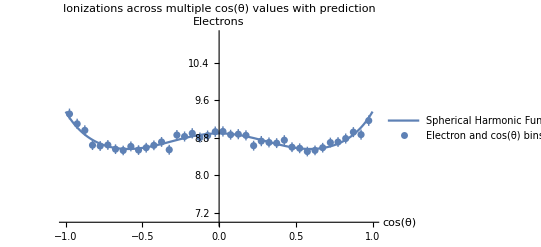

```mathematica
Show[Plot[fit[ArcCos[theta],0],{theta,-1,1},PlotRange->{7,11},PlotLegends->{"Spherical Harmonic Function"}],ListPlot[electrons,PlotLegends->{"Electron and cos(θ) bins "},PlotRange->{7,11}],AxesLabel->{"cos(θ)",Electrons},PlotLabel->"Ionizations across multiple cos(θ) values with prediction"]
```

```mathematica
MaxElectrons[potential_,Ni_,a_,b_,h_,lmax_,reps_]:= Module[{idx,errors,electronsPart,list, bins,i,thetaslist,constants,SHYs,fit,max,error},
bins =Last[Last[Last[Reap[SCAvgElectrons3D[potential,a,b,h,Ni,0.2,lmax,reps]]]]];
errors =Sqrt[bins[[3]]/bins[[1]] -(bins[[2]]/bins[[1]])^2]/Sqrt[reps];
electronsPart=Table[Around[(bins[[2]]/bins[[1]])[[i]],errors[[i]]],{i,1,10}];
list = bins[[6]];
fit=LinearModelFit[list,Table[SphericalHarmonicY[l,0,θ,ϕ],{l,0,lmax,2}],{θ,ϕ},IncludeConstantBasis->False];
Clear[t];
max=NMaximize[fit[t,0],{t,0,Pi}];
SHYs=Table[SphericalHarmonicY[l,0,t,0],{l,0,lmax,2}];
error = Sqrt[SHYs.fit["CovarianceMatrix"].Transpose[SHYs]]/.max[[2]];
(*Print[Plot[fit[ArcCos[theta],0],{theta,-1,1},PlotRange->{0,max[[1]]+3}]];
Print[ListPlot[Transpose[{Table[theta,{theta,-0.9,0.9,0.2}],electronsPart}],PlotRange->{0,max[[1]]+3}]];*)
Around[max[[1]],error]
]
```

```mathematica
MaxElectrons[potential,13,2,9,18,6,2000]
```

15.51.0

```mathematica
MaxElectrons[potential,15,2,9,18,6,2000]
```

18.31.4

```mathematica
MaxElectrons[potential,17,2,9,18,6,2000]
```

22.91.6

```mathematica
MaxElectrons[potential,19,2,9,18,6,2000]
```

28.72.3

```mathematica
MaxElectrons[potential,21,2,9,18,6,2000]
```

32.82.4

```mathematica
MaxElectrons[potential,23,2,9,18,6,2000]
```

40.63.1

{{13,15.51.0},{15,18.31.4},{17,22.91.6},{19,28.72.3},{21,32.82.4},{23,40.63.1}}

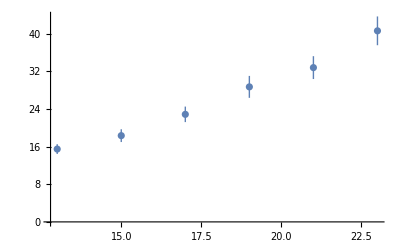

```mathematica
maxes = {{13,15.51.0},{15,18.31.4},{17,22.91.6},{19,28.72.3},{21,32.82.4},{23,40.63.1}}
ListPlot[maxes]
```

```mathematica
nis = #[[1]]&/@maxes;
vals= #[[2]]&/@maxes;
electrons=#[[1]]&/@vals;
list=Transpose[{nis,electrons}];
fit=[list,x,x]
sol = 1/a(25-b) /.{a->fit["BestFitParameters"][[2]],b->fit["BestFitParameters"][[1]]};
Clear[a,b];
f=1/a(25-b);
error=Sqrt[{D[f,b],D[f,a]}.fit["CovarianceMatrix"].Transpose[{D[f,b],D[f,a]}]]/.{a->fit["BestFitParameters"][[2]],b->fit["BestFitParameters"][[1]]};
result=Around[sol,error]
```

FittedModel[-18.5113+2.49887 x]

17.410.24

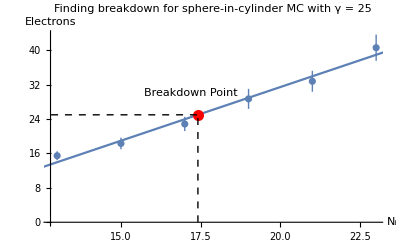

```mathematica
Show[ListPlot[maxes],Plot[fit[x],{x,10,25}],Graphics[{Red,PointSize[0.02],Point[{result[[1]],25}]}],Graphics[{Dashed,Black,Line[{{12.81,25},{result[[1]],25}}],Line[{{result[[1]],0},{result[[1]],25}}]}],Graphics[Text[Breakdown Point,{17.2,30}]],AxesLabel->{Subscript[N,i],Electrons},PlotLabel->"Finding breakdown for sphere-in-cylinder MC with γ = 25"]
```

## Sphere-in-cylinder breakdown plotting

```mathematica
FindBreakdownSC[a_,b_,h_,Ni0_,γ_,reps_]:=Module[{region,lapl,potential,maxes,i,errors,list,max,params,fit,error,p1,p2,f,vals,errorslist,listForFit},
region = RegionDifference[Cylinder[{{0,0,-h/2},{0,0,h/2}},b],Ball[{0,0,0},a]];lapl= Laplacian[f[x,y,z],{x,y,z}] == 0;potential = NDSolveValue[{lapl, DirichletCondition[f[x,y,z] ==1,x^2+y^2+z^2<a^2], DirichletCondition[f[x,y,z] == 0, x^2+y^2+z^2≥a^2]},f, {x,y,z}∈region,AccuracyGoal->4];
maxes = Table[{Ni,MaxElectrons[potential,Ni,a,b,h,6,reps]},{Ni,Ni0-4,Ni0+2,2}];
Print[maxes];
listForFit = {#[[1]],#[[2,1]]}&/@maxes;
errorslist = #[[2,2]]&/@maxes;
fit=LinearModelFit[listForFit,x,x,Weights->1/errorslist^2];
f=1/p1(γ-p2);
error={D[f,p2],D[f,p1]}.fit["CovarianceMatrix"].Transpose[{D[f,p2],D[f,p1]}]/.{p1->fit["BestFitParameters"][[2]],p2->fit["BestFitParameters"][[1]]};
Around[f,Sqrt[error]]/.{p1->fit["BestFitParameters"][[2]],p2->fit["BestFitParameters"][[1]]}
]
```

```mathematica
FindBreakdownSC[5,10,20,20,25,1000]
```

20.80.7

```mathematica
FindBreakdownSC[10,20,40,20,25,1000]
```

14.40.4

```mathematica
FindBreakdownSC[15,30,60,15,25,500]
```

12.670.20

```mathematica
FindBreakdownSC[20,40,80,15,25,500]
```

12.70.4

```mathematica
FindBreakdownSC[23,46,92,13,25,500]
```

13.00.5

```mathematica
FindBreakdownSC[25,50,100,13,25,400]
```

13.150.13

```mathematica
FindBreakdownSC[30,60,120,11,25,50]
```

14.52.5

```mathematica
FindBreakdownSC[7,14,28,18,25,600]
```

15.40.4

```mathematica
FindBreakdownSC[4.125,8.25,16.5,30,25,2000]
```

43.91.8

```mathematica
bdvals = {{4.125,Around[43.9,1.8]},{5,Around[20.8,0.7]},{7.25,Around[15.4,0.4]},{10,Around[14.4,0.4]},{15,Around[12.67,0.2]},{20,Around[12.7,0.4]},{25,Around[13.15,0.13]},{30,Around[14.5,0.8]}}
```

{{4.125,43.91.8},{5,20.80.7},{7.25,15.40.4},{10,14.40.4},{15,12.670.20},{20,12.70.4},{25,13.150.13},{30,14.50.8}}

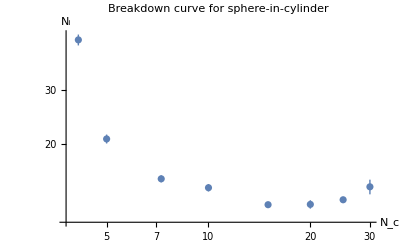

```mathematica
ListLogLogPlot[bdvals,AxesLabel->{Subscript[N,c],Subscript[N,i]},PlotLabel->"Breakdown curve for sphere-in-cylinder"]
```

## Plotting fusor data

```mathematica
data=Import["/Users/wbowers/Downloads/RAWpaschendata.txt","Table"]
```

{{----------,--------},{17.4373,2086.77},{17.4627,2052.92},{17.4878,2069.5},{17.5153,2036.34},{17.549,2081.93},{17.5836,2041.17},{17.6141,2037.03},{17.641,2048.08},{17.6684,2031.5},7155,{16663.4,2073.64},{16666.9,2081.24},{16670.7,2081.24},{16677.3,2079.17},{16684,2102.66},{16690.9,2073.64},{16697.9,2077.79},{16704.9,2082.62},{----------,--------}}
 |  |  |  |

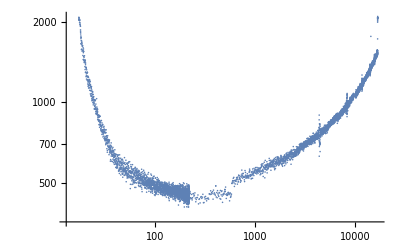

```mathematica
ListLogLogPlot[data]
```

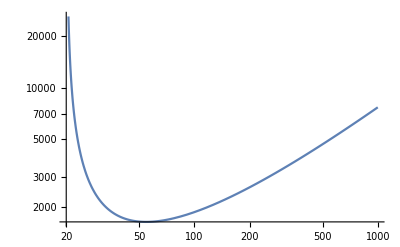

```mathematica
LogLogPlot[30x/(Log[x]-3),{x,20,1000}]
```

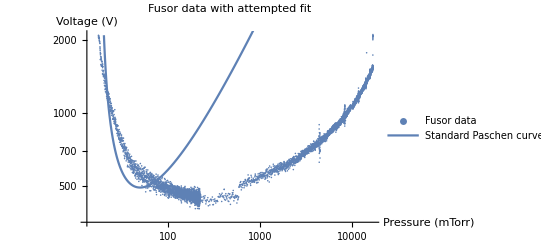

```mathematica
Show[ListLogLogPlot[data,PlotLegends->{"Fusor data"}],LogLogPlot[10x/(Log[x]-2.9),{x,20,1000},PlotLegends->{"Standard Paschen curve"}],AxesLabel->{"Pressure (mTorr)","Voltage (V)"},PlotLabel->"Fusor data with attempted fit"]
```

## Visualizing geometries

```mathematica
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0},5]}],Graphics3D[{Opacity[0.5],Sphere[{0,0,0},2]}],Graphics3D[{Thick,Dashed,Red,Line[{{0,0,0},{5,0,1}}]}],Graphics3D[{Thick,Dashed,Blue,Line[{{0,0,0},{2,0,-0.5}}]}],Graphics3D[{Text[Style["a",Larger,Italic],{0.75,0,-0.75}],Text[Style["b",Larger,Italic],{3.25,0,1.25}]}],PlotLabel->"Visualization of Concentric Spheres Setup",AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{Opacity[0.5],Cylinder[{{0,0,-5},{0,0,5}},5]}],Graphics3D[{Opacity[0.5],Sphere[{0,0,0},2]}],Graphics3D[{Thick,Dashed,Red,Line[{{0,0,0},{5,0,0}}]}],Graphics3D[{Thick,Dashed,Blue,Line[{{0,0,0},{2,0,-0.5}}]}],Graphics3D[{Thick,Dashed,Purple,Line[{{0,0,0},{0,0,5}}]}],Graphics3D[{Text[Style["a",Larger,Italic],{0.75,0,-0.75}],Text[Style["b",Larger,Italic],{3.25,0,0.65}],Text[Style["h",Larger,Italic],{0.5,0,3}]}],PlotLabel->"Visualization of Sphere-in-Cylinder Setup",AxesLabel->Automatic]
```

-Graphics3D-